```mathematica
Clear["Global`*"]
```

```mathematica
ar=2 0.5;(*aspect ratio*)
ntheta=40;
nphi=ar ntheta/2;
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,LogLogPlot,ListLinePlot,ListLogLogPlot},Frame->True,Axes->False,GridLines->None,ImageSize->500,(*Apply the high-contrast colors and thickness*)PlotStyle->(Directive[AbsoluteThickness[1.5]]),(*Force deep black frame and tick numbers*)FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontSize->18],(*Base style for any text that isn't MaTeX*)BaseStyle->{FontFamily->"Latin Modern Roman 12",FontSize->18}];
```

```mathematica
SetOptions[MaTeX,"FontSize"->18];
```

```mathematica
symboliclegendre[n_,x_]:=Solve[LegendreP[n,x]==0];
legendreprime[n_,a_]:=D[LegendreP[n,x],x]/. x->a;
weights[n_,x_]:=2/((1-x^2) legendreprime[n,x]^2);
```

```mathematica
xlist=x/.symboliclegendre[ntheta,x];
roots=N[xlist,15];
```

```mathematica
nodes=π/2(roots+1);
wgtsTheta=N[π/2 weights[ntheta,xlist],15];
```

```mathematica
tstFn[x_]:=(1/(1/100+(x-3/10)^2)+1/(1/25+(x-9/10)^2)-6)
```

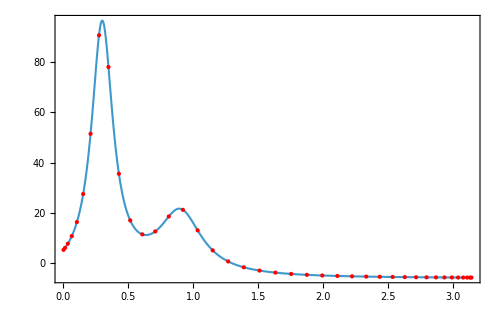

```mathematica
Plot[tstFn[x],{x,0,π},PlotRange->All,Epilog->{PointSize[Medium],Red,Point[Transpose[{nodes,Map[tstFn,nodes]}]]}]
```

```mathematica
NIntegrate[tstFn[x],{x,0,π}]
wgtsTheta.Map[tstFn,nodes]
```

23.1668

23.15674771719

```mathematica
8 6  8 6
```

2304

```mathematica
384 3
```

1152

```mathematica
2304/3
```

768

```mathematica
48 48
```

2304

```mathematica
phiPt=Table[(2π)/nphi(j-1),{j,1,nphi}]//N;
thetaPt=Table[π/2(1+roots[[i]]),{i,1,ntheta}];
```

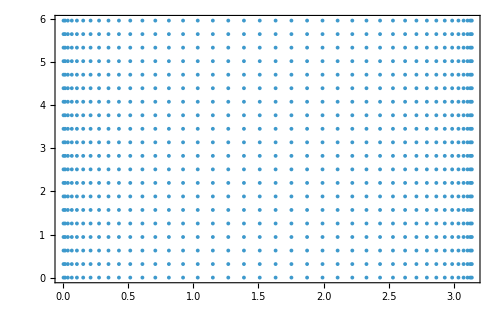

```mathematica
parametricPt=Tuples[{thetaPt,phiPt}//N];
ListPlot[parametricPt]
```

```mathematica
(*Parametric equation of surface (spheroid):*)
x1=ar Sin[parametricPt[[All,1]]] Cos[parametricPt[[All,2]]];
x2=ar Sin[parametricPt[[All,1]]] Sin[parametricPt[[All,2]]];
x3=Cos[parametricPt[[All,1]]];
```

```mathematica
collocationPt=Transpose[{x1,x2,x3}];
```

```mathematica
Graphics3D[{Point[collocationPt]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*set normal vectors associated with each collocation point: eTheta x ePhi*)
rVec={ar Sin[theta] Cos[phi],ar Sin[theta] Sin[phi],Cos[theta]};(*for spheroids*)
eTheta=D[rVec,theta];
ePhi=D[rVec,phi];
nVec=Cross[eTheta,ePhi]//Simplify;(*not a unit vector...its magnitude carry jacobian factor*)
```

```mathematica
normalVec=Table[nVec/.{theta->parametricPt[[m,1]],phi->parametricPt[[m,2]]},{m,1,Length@parametricPt}];
```

```mathematica
Min[Map[Norm,normalVec]] (*make sure all normalVectors are normalizable!*)
```

0.0027682

```mathematica
Graphics3D[{Point[collocationPt],Table[Arrow[{collocationPt[[k]],collocationPt[[k]]+0.6Normalize@normalVec[[k]]}],{k,1,Length@collocationPt,1}]}]
```

-Graphics3D-

```mathematica
wgtPt=Tuples[{wgtsTheta ,2 π/nphi Table[1,nphi]}//N];(*uniform wgts for trapezoidal rule*)
```

```mathematica
wgtPt[[1;;10]]
wgtPt//Dimensions
```

{{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159},{0.121746,0.314159}}

{800,2}

```mathematica
wgtVec=wgtPt[[All,1]]wgtPt[[All,2]] Map[Norm,normalVec];
```

```mathematica
wgtVec//Dimensions
```

{800}

```mathematica
(*surface integral of f(x)=f(collocationPts).wgtVec*)
NumberForm[N[Total[wgtVec],15],15]
```

12.5663706143592

```mathematica
NumberForm[N[Total[wgtVec collocationPt[[All,2]]^2],15],15]
```

4.18879020478639

```mathematica
reg=ParametricRegion[{ar Sin[theta] Cos[phi],ar Sin[theta] Sin[phi],Cos[theta]},{{theta,0,π},{phi,0,2π}}];
```

```mathematica
(*Region[reg]*)
```

```mathematica
NIntegrate[y^2,{x,y,z}∈reg,AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15]
```

4.18879020478641

```mathematica
NumberForm[2π 0.5^2(1+1/(0.5 e)ArcSin[e])/.e->√(1-0.5^2),15]
```

5.36960883197093

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\cloudData\PhDWork\year2\bimBoundedSpectral\postProcess

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\sphereCPLess.txt",collocationPt,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\sphereCPLess.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\sphereNVecLess.txt",Map[Normalize,normalVec],"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\sphereNVecLess.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\sphereWgtsLess.txt",wgtVec,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\sphereWgtsLess.txt

### For container:

```mathematica
Lbox = 2 125;(*length of the box*)
nY=128;
nphi=40;(*40*)
```

```mathematica
nY nphi
```

5120

```mathematica
xlist=x/.symboliclegendre[nY,x];
roots=N[xlist,15];
nodes=Lbox/2(roots);
wgtsTheta=N[Lbox/2 weights[nY,xlist],15];
```

```mathematica
phiPt=Table[(2π)/nphi(j-1),{j,1,nphi}]//N;
thetaPt=Table[(Lbox/2 roots[[i]]),{i,1,nY}];
```

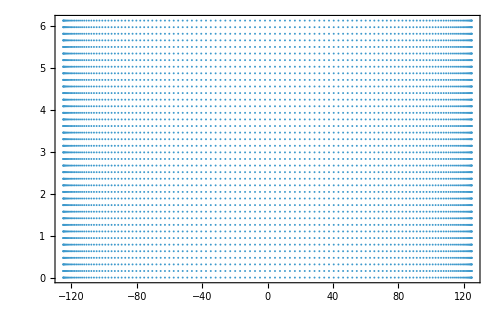

```mathematica
parametricPt=Tuples[{thetaPt,phiPt}//N];
ListPlot[parametricPt]
```

```mathematica
Lbox/2
```

125

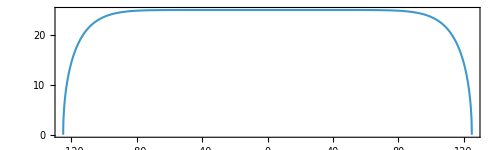

```mathematica
kappa=1;
rad=25;
borderFn[x_]:=rad √(1-((2x)/Lbox)^10);
Plot[borderFn[x],{x,-Lbox/2,Lbox/2},PlotRange->All(*,Epilog->{PointSize[Medium],Red,Point[Transpose[{nodes,Map[borderFn,nodes]}]]}*),AspectRatio->0.3,FrameLabel->{MaTeX["z/a"],MaTeX["x/a"]}]
```

```mathematica
Show[ParametricPlot3D[{borderFn[Lbox/2 Cos[th]] Cos[phi],borderFn[Lbox/2 Cos[th]] Sin[phi],Lbox/2 Cos[th]},{th,0,π},{phi,0,2π},PlotStyle->Opacity[0.4],ImageSize->Medium,Mesh->None,Axes->True,Ticks->None,AxesLabel->{"x","y","z"}],
Graphics3D[{Opacity[1],Cuboid[{0,0,-Lbox/2},{1.4rad,0.01,Lbox/2}]}]
]
```

-Graphics3D-

```mathematica
uContainer[x_]:=0(1-borderFn[x]^2/(rad)^2){0,1,0};
```

```mathematica
(*Parametric equation of container:*)
xC1=borderFn[parametricPt[[All,1]]] Cos[parametricPt[[All,2]]];
xC3=borderFn[parametricPt[[All,1]]] Sin[parametricPt[[All,2]]];
xC2=parametricPt[[All,1]];
```

```mathematica
boxCollocationPt=Transpose[{xC1,xC2,xC3}];
```

```mathematica
Graphics3D[{Point[boxCollocationPt],Sphere[{-1.25,0,0},1],Sphere[{1.25,0 27,0},1]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
uContainerList=Map[uContainer,boxCollocationPt[[All,2]]];
```

```mathematica
uContainerList//Dimensions
```

{5120,3}

```mathematica
(*set normal vectors associated with each collocation point: eTheta x ePhi*)
rCVec={borderFn[y] Cos[phi],y,borderFn[y] Sin[phi]};(*for spheroids*)
eCTheta=D[rCVec,y];
eCPhi=D[rCVec,phi];
nCVec=-Cross[eCTheta,eCPhi]//Simplify;(*not a unit vector...its magnitude carry jacobian factor*)
```

```mathematica
boxNormalVec=Table[nCVec/.{y->parametricPt[[m,1]],phi->parametricPt[[m,2]]},{m,1,Length@parametricPt}]//N;
```

```mathematica
Min@Map[Norm,boxNormalVec]
Max@Map[Norm,boxNormalVec]
```

22.1776

25.

```mathematica
Graphics3D[{Point[boxCollocationPt],Table[Arrow[{boxCollocationPt[[k]],boxCollocationPt[[k]]+20Normalize@boxNormalVec[[k]]}],{k,1,Length@boxCollocationPt,50}]}]
```

-Graphics3D-

```mathematica
wgtCPt=Tuples[{wgtsTheta,2 π/nphi Table[1,nphi]}//N];(*uniform wgts for trapezoidal rule*)
```

```mathematica
wgtCPt[[1;;10]]
wgtCPt//Dimensions
```

{{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708},{3.05577,0.15708}}

{5120,2}

```mathematica
boxWgtVec=wgtCPt[[All,1]]wgtCPt[[All,2]] Map[Norm,boxNormalVec];
```

```mathematica
boxWgtVec//Dimensions
```

{5120}

```mathematica
(*surface integral of f(x)=f(collocationPts).wgtVec*)
NumberForm[Total[boxWgtVec],15]
```

38487.7131881135

```mathematica
NIntegrate[Norm[nCVec],{y,-Lbox/2,Lbox/2},{phi,0,2π}]
```

38487.7

```mathematica
(*reg=ParametricRegion[{borderFn[u]Cos[v],borderFn[u]Sin[v],u},{{u,-Lbox/2,Lbox/2},{v,0,2π}}];*)
(*Region[reg]*)
```

```mathematica
boxCollocationPt//Dimensions
```

{5120,3}

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxCollocationPtsTst.txt",boxCollocationPt,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxCollocationPtsTst.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxNormalVectorsTst.txt",Map[Normalize,boxNormalVec],"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxNormalVectorsTst.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxWgtsTst.txt",boxWgtVec,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxWgtsTst.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxVelTst.txt",uContainerList,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxVelTst.txt

```mathematica
40 128
```

5120

```mathematica
1/(6π)//N
```

0.0530516